```mathematica
Clear["Global`*"]
rp=0.1; (* used for radius in polar *)
xp=rp*Cos[t]; (* used for x-coord in polar *)
yp=rp*Sin[t]; (* used for y-coord in polar *)
Index[p_,q_]:=1/(2π)N[Integrate[Re[(p D[q,t]-q D[p,t])/(p^2+q^2)],{t,0,2π}]];
a = 2;
```

Use Poincare-Bendixson Theorem to find and classify limit cycles for Problem 1 and Problem 2.

Problem 1

```mathematica
(* x_dot = x-y-x^3 *)
(* y_dot = x+y-y^3 *)
(xp-yp-xp^3)D[xp+yp-yp^3,t]-(xp+yp-yp^3)D[xp-yp-xp^3,t]//FullSimplify
(xp-yp-xp^3)^2+(xp+yp-yp^3)^2//FullSimplify
1/(2π)Integrate[((0.019850375000000003)+0.00004962500000000002 Cos[4 t]-0.00005000000000000002 Sin[4 t])/(0.019850625-0.000049625000000000014 Cos[4 t]+0.000050000000000000016 Sin[4 t]),{t,0,2π}] (* I had to get the intgrand in this form in order to integrate since the computer did not know how to handle numerical 0 as seen in the immidiate outputs 1 and 2 below *)
```

(0.0198504+1.73472×10^-18 ⅈ)+0.000049625 Cos[4 t]-0.00005 Sin[4 t]

0.0198506+7.86047×10^-19 Cos[2 t]-0.000049625 Cos[4 t]+0.00005 Sin[4 t]

1.

Having an index of 1 indicates (x_dot,y_dot) is stable, or unstable, has a node or focus at the origin.

-1/4 r1 (-4+3 r1^2+r1^2 Cos[4 t])

1+1/4 r1^2 Sin[4 t]

r1==0.||r1==1.1547||r1==-1.1547

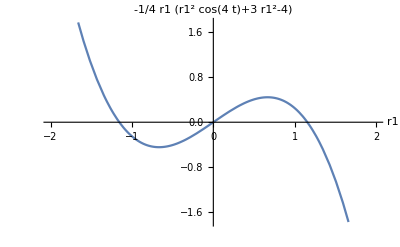

r1==0.+2. ⅈ||r1==0.-2. ⅈ

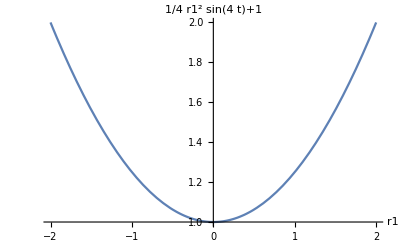

```mathematica
x1=r1 Cos[t];
y1=r1 Sin[t];
x1dot = x1-y1-x1^3;
y1dot = x1+y1-y1^3;
r1dot=(x1 x1dot+y1 y1dot)/r1//FullSimplify
theta1dot=(x1 y1dot-y1 x1dot)/r1^2//FullSimplify
N[Roots[r1dot==0/.t->π/8,r1]]
Plot[r1dot/.t->π/8,{r1,-a,a},AxesLabel->{r1,r1dot}]
N[Roots[theta1dot==0/.t->π/8,r1]]
Plot[theta1dot/.t->π/8,{r1,-a,a},AxesLabel->{r1,theta1dot}]
```

Note that both phase plane plots above are for t = π/8 and change in time, but all have the same general behavior.

We now have four regions to consider for the second phase plane plot above, but we only need to consider two regions (in quadrants 1 and 4) since the plot is symmetric.
The first region indicates that the point r1 = 0 is a stable equilibrium and r1 = 1.1547 is an unstable equilibrium.
(But this does not make sense based on further analysis of the plots.)

We now have two regions to consider for the second phase plane plot above.
The first region indicates that if a test particle were placed in the region 0 < r1 < 1.1547, it will have a positive and decreasing angular velocity with respect to r1 until it is close enough to r1 = 1.1547 in which case the test particle would then tend towards a constant angular velocity with respect to r1.
The second region indicates that if a test particle were placed in the region 1.1547 < r1 < ∞, it will have a negative and increasing angular velocity with respect to r1 until it is close enough to r1 = 1.1547 in which case the test particle would then tend towards a constant angular velocity with respect to r1.

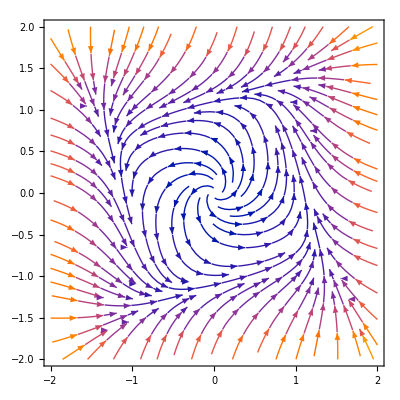

```mathematica
StreamPlot[{x-y-x^3,x+y-y^3},{x,-a,a},{y,-a,a},Axes->True]
```

The above plot of (x_dot,y_dot) shows that “squared-off” circle about the origin is a stable limit cycle.

Problem 2

```mathematica
(* with r^2 = x^2 + y^2 *)
(* x_dot = -y+x(r^4-3 r^2+1) *)
(* y_dot = x+y(r^4-3 r^2+1) *)
Index[-yp+xp(rp^4-3 rp^2+1),xp+yp(rp^4-3 rp^2+1)]
```

1.

Having an index of 1 indicates (x_dot,y_dot) is stable, or unstable, has a node or focus at the origin.

r2-3 r2^3+r2^5

1

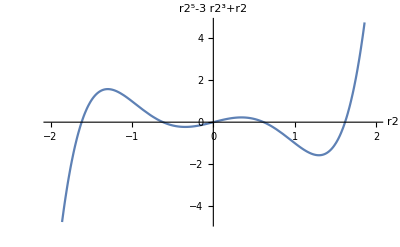

r2==0.||r2==-1.61803||r2==0.618034||r2==-0.618034||r2==1.61803

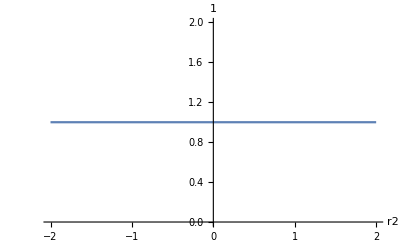

False

```mathematica
$Assumptions = r2>0;
x2=r2 Cos[t];
y2=r2 Sin[t];
x2dot = -y2+x2(r2^4-3 r2^2+1);
y2dot = x2+y2(r2^4-3 r2^2+1);
r2dot=(x2 x2dot+y2 y2dot)/Sqrt[x2^2+y2^2]//FullSimplify
theta2dot=(x2 y2dot-y2 x2dot)/(x2^2+y2^2)//FullSimplify
Plot[r2dot,{r2,-a,a},AxesLabel->{r2,r2dot}]
N[Roots[r2dot==0,r2]]
Plot[theta2dot,{r2,-a,a},AxesLabel->{r2,theta2dot}]
N[Roots[theta2dot==0,r2]]
$Assumptions=True;
```

The first phase plane plot above shows that r2 = 0 is a stable equilibrium.
(But this does not make sense based on further analysis of the plots.)

We now have three regions to consider for the second phase plane plot above.
The first region indicates that if a test particle were placed in the region 0 < r2 < 0.618034, it will have a positive and decreasing angular velocity with respect to r2 until it reaches r2 = 0.618034; upon reaching r2, the test particle would then tend towards a constant angular velocity with respect to r2.
The second region indicates that if a test particle were placed in the region 0.618034 < r2 < 1.61803, it will have a negative and increasing angular velocity with respect to r2 until it reaches r2 = 0.618034; upon reaching r2, the test particle would then tend towards a constant angular velocity with respect to r2.
The third region indicates that if a test particle were placed in the region 1.61803 < r2 < ∞, it will have a positive and increasing angular velocity with respect to r2 never reaching a limit cycle.

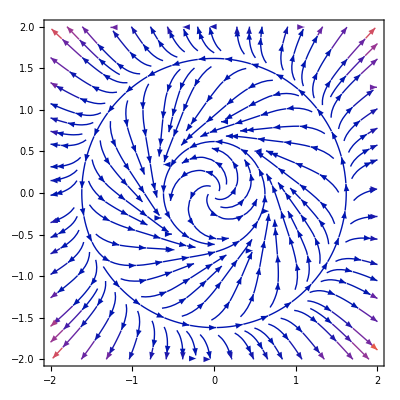

```mathematica
r=Sqrt[x^2+y^2];
StreamPlot[{-y+x(r^4-3 r^2+1),x+y(r^4-3 r^2+1)},{x,-a,a},{y,-a,a},Axes->True]
```

The above plot of (x_dot,y_dot) shows that there are two limit cycles about the origin, the first being the circle of smaller radius is a stable limit cycle and the second being the circle of larger radius is an unstable limit cycle.